```mathematica
(*Spin Wheel Animation*)
Graphics3D[{
(*Ground*)
Gray,Cuboid[{0,0,0},{100,70,5}],
(*Background*)
White,Cuboid[{0,65,0},{100,70,70}],

(*Spin Wheel*)
Red,Cylinder[{{30,32,43},{30,35,43}},17],
Pink,Cylinder[{{30,27,43},{30,30,43}},3],
Yellow,Cylinder[{{30,35,43},{30,30,43}},15],
Green,Polygon[{{16,29,43},{20,29,52},{27,29,43}}],
Blue,Polygon[{{20,29,33},{28,29,40},{28,29,29}}],
Orange,Polygon[{{33,29,42},{44,29,42},{40,29,34}}],
Red,Polygon[{{32,29,57},{31,29,46},{40,29,53}}],

(*Stand*)
Black,Cuboid[{15,32,5},{45,15,25}],
Gray,Cuboid[{10,50,5},{50,35,70}],
White,Cuboid[{20,14,15},{28,10,20}],
Black,Cuboid[{23,9,17},{25,9,19}],

(*Handle*)
Black,Tube[{{45,25,15},{55,25,15}},0.8],
Black,Tube[{{55,25,15},{55,25,25}},0.8],
Red,Sphere[{55,25,28},3],

(*Lights*)
White,Cuboid[{15,34,62},{45,30,65}]
}
]
```

-Graphics3D-

```mathematica
scene1=Table[Graphics3D[{
(*Ground*)
Gray,Cuboid[{0,0,0},{100,70,5}],
(*Background*)
White,Cuboid[{0,65,0},{100,70,70}],
(*Spin Wheel*)
Red,Cylinder[{{30,32,43},{30,35,43}},17],
Pink,Cylinder[{{30,27,43},{30,30,43}},3],
Yellow,Cylinder[{{30,35,43},{30,30,43}},15],
Green,Polygon[{{16,29,43},{20,29,52},{27,29,43}}],
Blue,Polygon[{{20,29,33},{28,29,40},{28,29,29}}],
Orange,Polygon[{{33,29,42},{44,29,42},{40,29,34}}],
Red,Polygon[{{32,29,57},{31,29,46},{40,29,53}}],
(*Stand*)
Black,Cuboid[{15,32,5},{45,15,25}],
Gray,Cuboid[{10,50,5},{50,35,70}],
White,Cuboid[{20,14,15},{28,10,20}],
Black,Cuboid[{23,9,17},{25,9,19}],
(*Handle*)
Black,Tube[{{45,25,15},{55,25,15}},0.8],
Rotate[
{{Black,Tube[{{55,25,15},{55,25,25}},0.8]},Red,Sphere[{55,25,28},3]},Sin[x/4],{1,0,0},{55,25,15}],
(*Lights*)
White,Cuboid[{15,34,62},{45,30,65}]
}
],{x,0,7}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
scene2=Table[Graphics3D[{
(*Ground*)
Gray,Cuboid[{0,0,0},{100,70,5}],
(*Background*)
White,Cuboid[{0,65,0},{100,70,70}],
(*Spin Wheel*)
Red,Cylinder[{{30,32,43},{30,35,43}},17],
Rotate[{Pink,Cylinder[{{30,27,43},{30,30,43}},3],
Yellow,Cylinder[{{30,35,43},{30,30,43}},15],
Green,Polygon[{{16,29,43},{20,29,52},{27,29,43}}],
Blue,Polygon[{{20,29,33},{28,29,40},{28,29,29}}],
Orange,Polygon[{{33,29,42},{44,29,42},{40,29,34}}],
Red,Polygon[{{32,29,57},{31,29,46},{40,29,53}}]},x,{0,1,0},{30,37,43}],
(*Stand*)
Black,Cuboid[{15,32,5},{45,15,25}],
Gray,Cuboid[{10,50,5},{50,35,70}],
White,Cuboid[{20,14,15},{28,10,20}],
Black,Cuboid[{23,9,17},{25,9,19}],
(*Handle*)
Black,Tube[{{45,25,15},{55,25,15}},0.8],
{Black,Tube[{{55,25,15},{55,25,25}},0.8]},Red,Sphere[{55,25,28},3],
(*Lights*)
White,Cuboid[{15,34,62},{45,30,65}]
}
],{x,0,10}]
```

```mathematica
scene3=Table[Graphics3D[{
(*Ground*)
Gray,Cuboid[{0,0,0},{100,70,5}],
(*Background*)
White,Cuboid[{0,65,0},{100,70,70}],
(*Spin Wheel*)
Red,Cylinder[{{30,32,43},{30,35,43}},17],
Pink,Cylinder[{{30,27,43},{30,30,43}},3],
Yellow,Cylinder[{{30,35,43},{30,30,43}},15],
Green,Polygon[{{16,29,43},{20,29,52},{27,29,43}}],
Blue,Polygon[{{20,29,33},{28,29,40},{28,29,29}}],
Orange,Polygon[{{33,29,42},{44,29,42},{40,29,34}}],
Red,Polygon[{{32,29,57},{31,29,46},{40,29,53}}],
(*Stand*)
Black,Cuboid[{15,32,5},{45,15,25}],
Gray,Cuboid[{10,50,5},{50,35,70}],
White,Cuboid[{20,14,15},{28,10,20}],
Black,Cuboid[{23,9,17},{25,9,19}],
(*Handle*)
Black,Tube[{{45,25,15},{55,25,15}},0.8],
{Black,Tube[{{55,25,15},{55,25,25}},0.8]},Red,Sphere[{55,25,28},3],
(*Tickets*)
Yellow,Cuboid[{23,8,18},{25,5,18}],
Blue,Cuboid[{23,5,18},{25,3,18}],
Red,Cuboid[{23,3,18},{25,0,18}],
(*Lights*)
{RGBColor[Sin[x ],Cos[x ],Cos[x ]],Cuboid[{15,34,62},{45,30,65}]
}}
]
,{x,0,10}]


scene4=Table[Graphics3D[{
(*Ground*)
Gray,Cuboid[{0,0,0},{100,70,5}],
(*Background*)
White,Cuboid[{0,65,0},{100,70,70}],
(*Spin Wheel*)
Red,Cylinder[{{30,32,43},{30,35,43}},17],
Pink,Cylinder[{{30,27,43},{30,30,43}},3],
Yellow,Cylinder[{{30,35,43},{30,30,43}},15],
Green,Polygon[{{16,29,43},{20,29,52},{27,29,43}}],
Blue,Polygon[{{20,29,33},{28,29,40},{28,29,29}}],
Orange,Polygon[{{33,29,42},{44,29,42},{40,29,34}}],
Red,Polygon[{{32,29,57},{31,29,46},{40,29,53}}],
(*Stand*)
Black,Cuboid[{15,32,5},{45,15,25}],
Gray,Cuboid[{10,50,5},{50,35,70}],
White,Cuboid[{20,14,15},{28,10,20}],
Black,Cuboid[{23,9,17},{25,9,19}],
(*Handle*)
Black,Tube[{{45,25,15},{55,25,15}},0.8],
{Black,Tube[{{55,25,15},{55,25,25}},0.8]},Red,Sphere[{55,25,28},3],
(*Tickets*)
Yellow,Cuboid[{23,8,18},{25,5,18}],
Blue,Cuboid[{23,5,18},{25,3,18}],
Red,Cuboid[{23,3,18},{25,0,18}],
(*Lights*)
Gray,Cuboid[{15,34,62},{45,30,65}]
,
(*Music Note*)
Translate[{Black,Sphere[{64,20,40},2],
Tube[{{65,20,40},{65,20,47},{71,20,47},{71,20,40}}],
Black,Sphere[{70,20,40},2]
},
{Piecewise[{{x,x≤ 100},{100,x>100}}],0,20Sin[x]}]
}
]
,{x,0,10}]
```

```mathematica
animation=Flatten[{scene1,scene2,scene3,scene4}];
```

### Scratch Work

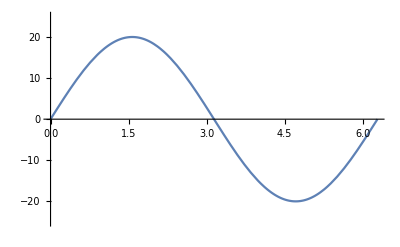

```mathematica
(*Sin Wave*)
Plot[20Sin[x],{x,0,2π}, PlotRange-> {{0,2π},{-25,25}}]
```

### Visualize

```mathematica
Dimensions[animation]
```

{41}

```mathematica
Manipulate[animation[[n]],{n,1,41,1}]
```

```mathematica
SetDirectory["G:\\"]
```

G:\

```mathematica
Export["Chen_Peilin_B1.gif",animation]
```

Chen_Peilin_B1.gif